0.0056+(0.000013-0.000317 t) Cos[t]+(3.7×10^-7+7.×10^-7 t) Sin[t]+ⅇ^(0.2 t) (0.394 Cos[41.23 t]-0.0019 Sin[41.23 t])

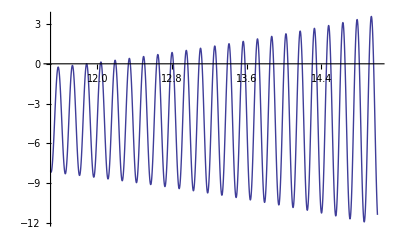

{t→12.6617}

```mathematica
Clear[x,t];
c1 = 0.394;
c2 = -0.0019;
x = ⅇ^(0.2 t)(c1 * Cos[41.23 t ] + c2 * Sin[41.23 t ]) + (-0.000317 t + 0.000013) Cos[t] + (0.0000007 t + 0.00000037) Sin[t] + 0.0056;
Print[x];
x0 = 4.245;
Plot[x -x0, {t,11.5,15}]
l = FindRoot[x - x0 , {t,11}];
Print[l];
```

```mathematica
Clear[t];
pr = D[x,t]
t = 12.6617;
pr
```

-0.000317 Cos[t]+(3.7×10^-7+7.×10^-7 t) Cos[t]+7.×10^-7 Sin[t]-(0.000013-0.000317 t) Sin[t]+ⅇ^(0.2 t) (-0.078337 Cos[41.23 t]-16.2446 Sin[41.23 t])+0.2 ⅇ^(0.2 t) (0.394 Cos[41.23 t]-0.0019 Sin[41.23 t])

-104.652